```mathematica
μ=0.05;
β=0.0001;
sol=NDSolve[{I0'[t]==-μ*I0[t]+S0[t]*β*I0[t],S0'[t]==-β*S0[t]*I0[t],S0[0]==1000,I0[0]==1},{I0,S0},{t,0,500}]
```

{{I0→InterpolatingFunction[…],S0→InterpolatingFunction[…]}}

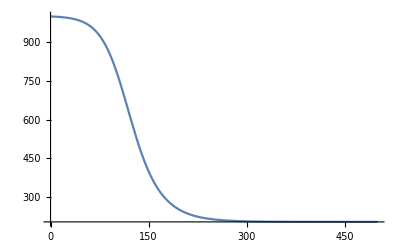

```mathematica
Plot[S0[t]/.sol,{t,0,500}]
```

```mathematica
Solve[{-β*SS*II==0,-(μ+r)*II+β*II*SS==0},{II,SS}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{II→0}}

```mathematica
ClearAll[R0,μ,β]
DSolve[{I0'[t]==-μ*I0[t]+S0[t]*β*I0[t],S0'[t]==-β*S0[t]*I0[t],R0'[t]==μ*I0[t],R0[0]==μ,S0[0]==-β*NN,I0[0]==-μ+β*NN},{I0,S0,R0},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvsing: Unable to resolve some of the arbitrary constants in the general solution using the given boundary conditions. It is possible that some of the conditions have been specified at a singular point for the equation.

{{S0→Function[{t},-1/βμ ProductLog[-1/μ ⅇ^(-(NN β^2-β μ-μ Log[-ⅇ^((NN β^2)/μ) NN β])/μ+(β InverseFunction[1/(K[1] (1+ProductLog[-(ⅇ^(-(NN β^2-β μ-μ Log[-ⅇ^((NN β^2)/μ) NN β])/μ+(β K[1])/μ) β)/μ]))K[1]1#1&][-t μ+1/(K[1] (1+ProductLog[-(ⅇ^(-C[1]/μ+(β K[1])/μ) β)/μ]))K[1]1NN β-μ])/μ) β]],I0→Function[{t},InverseFunction[1/(K[1] (1+ProductLog[-(ⅇ^(-(NN β^2-β μ-μ Log[-ⅇ^((NN β^2)/μ) NN β])/μ+(β K[1])/μ) β)/μ]))K[1]1#1&][-t μ+1/(K[1] (1+ProductLog[-(ⅇ^(-C[1]/μ+(β K[1])/μ) β)/μ]))K[1]1NN β-μ]],R0→Function[{t},μ+μ InverseFunction[1/(K[1] (1+ProductLog[-(ⅇ^(-(NN β^2-β μ-μ Log[-ⅇ^((NN β^2)/μ) NN β])/μ+(β K[1])/μ) β)/μ]))K[1]1#1&][-μ K[2]+1/(K[1] (1+ProductLog[-(ⅇ^(-C[1]/μ+(β K[1])/μ) β)/μ]))K[1]1NN β-μ]K[2]1t-μ InverseFunction[1/(K[1] (1+ProductLog[-(ⅇ^(-(NN β^2-β μ-μ Log[-ⅇ^((NN β^2)/μ) NN β])/μ+(β K[1])/μ) β)/μ]))K[1]1#1&][-μ K[2]+1/(K[1] (1+ProductLog[-(ⅇ^((β K[1])/μ-(NN β^2-β μ-μ Log[-ⅇ^((NN β^2)/μ) NN β])/μ) β)/μ]))K[1]1NN β-μ]K[2]10]}}

```mathematica
I0'[t_,I0_,I1_,I2_,S0_,μ_,β0_,r_] := -r*I0[t]-μ*I0[t]+S0[t]*β0*(I0[t]+I1[t]+I2[t])
I1'[t_,I0_,I1_,I2_,S1_,μ_,β1_,r_] := -r*I1[t]-μ*I1[t]+S1[t]*β1*(I0[t]+I1[t]+I2[t])
I2'[t_,I0_,I1_,I2_,S2_,μ_,β1_,r_] := -r*I2[t]-μ*I2[t]+S2[t]*β1*0.5*(I0[t]+I1[t]+I2[t])

S0Prime[t_,I0_,I1_,I2_,S0_,μ_,β0_,r_,B_]:=-S0[t]*β0*(I0[t]+I1[t]+I2[t])
S1Prime[t_,I0_,I1_,I2_,S1_,μ_,β1_,r_,B_]:=-S1[t]*β1*(I0[t]+I1[t]+I2[t])
S2Prime[t_,I0_,I1_,I2_,S2_,μ_,β1_,r_,B_]:=-S2[t]*β1*0.5*(I0[t]+I1[t]+I2[t])

R0Prime[t_,I0_,I1_,I2_,S0_,μ_,β0_,r_]:=(r+μ)*I0[t]
R1Prime[t_,I0_,I1_,I2_,S1_,μ_,β1_,r_]:=(r+μ)*I1[t]
R2Prime[t_,I0_,I1_,I2_,S2_,μ_,β1_,r_]:=(r+μ)*I2[t]
```

```mathematica
Solve[0==-r*I0[t]-μ*I0[t]+S0[t]*β0*(I0[t]+I1[t]+I2[t])
```

```mathematica
(-S0[t]*β0*(I0[t]+I1[t]+I2[t])/
```

```mathematica
Solve[{0 ==-r*I0-μ*I0+S0*β0*(I0+I1+I2),
0== -r*I1-μ*I1+S1*β0*b*(I0+I1+I2),0== -r*I2-μ*I2+S2*β0*a*(I0+I1+I2),
0==B-S0*β0*(I0+I1+I2),0==B-S1*β0*b*(I0+I1+I2),0==B-S2*β0*a*(I0+I1+I2)},{S0,S1,S2,I0,I1,I2}]
```

{{S0→(r+μ)/(3 β0),S1→(r+μ)/(3 b β0),S2→(r+μ)/(3 a β0),I0→B/(r+μ),I1→B/(r+μ),I2→B/(r+μ)}}

```mathematica
FullSimplify[(S1Prime[t,I0,I1,I2,S0,μ,β1,r,B]+S2Prime[t,I0,I1,I2,S1,μ,β1,r,B]+S0Prime[t,I0,I1,I2,S2,μ,β0,r,B])/(R1Prime[t,I0,I1,I2,S0,μ,β0,r]+R2Prime[t,I0,I1,I2,S1,μ,β0,r]+R0Prime[t,I0,I1,I2,S2,μ,β0,r])]
```

(-1. β1 S0[t]-0.5 β1 S1[t]-1. β0 S2[t])/(r+μ)

```mathematica
DSolve[S0'[R] == (-β S0[R])/(r+μ), {S0},R]
```

{{S0→Function[{R},ⅇ^(-(R β)/(r+μ)) C[1]]}}

```mathematica
Clear[β,μ,r,β2,β0,β1]
```

```mathematica
FullSimplify[ s0*ⅇ^(-(rf β0)/(r+μ)) +2*(Sqrt[s0])*(1-Sqrt[s0])*ⅇ^(-(rf β1)/(r+μ)) +(1-Sqrt[s0])^2*ⅇ^(-(rf β2)/(r+μ))]
```

ⅇ^(-(rf β2)/(r+μ)) (-1+√s0)^2+ⅇ^(-(rf β1)/(r+μ)) (2 √s0-2 s0)+ⅇ^(-(rf β0)/(r+μ)) s0

```mathematica
FullSimplify[Solve[1-rf == (-1+√s0)^2+ⅇ^(-(rf β0)/(r+μ)) (2 √s0-s0)]]
```

Solve::useq: The answer found by Solve contains equational condition(s) {0==-1+√(1-rf)-√(2-2 Power[«2»]-rf),0==-1-√(1-rf)-√(2+2 Power[«2»]-rf)}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

{{rf→0},{μ→ConditionalExpression[-r+(rf β0)/(2 ⅈ π C[1]+Log[1-rf/(rf-2 √s0+s0)]), C[1]∈ℤ]},{rf→0,s0→0},{rf→0,s0→4},{s0→ConditionalExpression[2-2 √(1-rf)-rf, ],μ→ConditionalExpression[-r+(rf β0)/(2 ⅈ π C[1]+Log[1/4 (3-√(1-rf))]), ]},{s0→ConditionalExpression[2+2 √(1-rf)-rf, ],μ→ConditionalExpression[-r+(rf β0)/(2 ⅈ π C[1]+Log[1/4 (3+√(1-rf))]), ]}}

```mathematica
Clear[β0,r,μ]
```

```mathematica
FullSimplify[-((r+μ) ProductLog[-(ⅇ^(-β0/(r+μ)) s0 β0)/(r+μ)])/β0 +( r/(μ+r))(1+((r+μ) ProductLog[-(ⅇ^(-β0/(r+μ)) s0 β0)/(r+μ)])/β0 )]
```

r/(r+μ)-(μ ProductLog[-(ⅇ^(-β0/(r+μ)) s0 β0)/(r+μ)])/β0

```mathematica
s0Final[r_,μ_,β0_,s0_]:=r/(r+μ)-(μ ProductLog[-(ⅇ^(-β0/(r+μ)) s0 β0)/(r+μ)])/β0
```

```mathematica
s1Final[r_,μ_,β1_,s1_]:=r/(r+μ)-(μ ProductLog[-(ⅇ^(-β1/(r+μ)) s1 β1)/(r+μ)])/β1
```

```mathematica
s2Final[r_,μ_,β2_,s2_]:=r/(r+μ)-(μ ProductLog[-(ⅇ^(-β2/(r+μ)) s2 β2)/(r+μ)])/β2
```

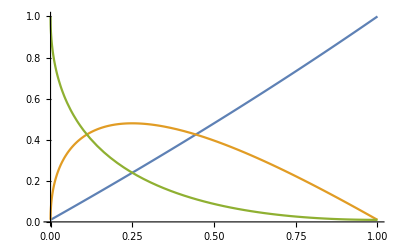

```mathematica
r=0.001;
β0 = 0.01;
μ = 0.1;
Plot[{s0Final[r,μ,β0,s0],s1Final[0.1*r,0.1*μ,0.1*β0,2*(s0^0.5)*(1-s0^0.5)],s2Final[0.05r,0.05μ,0.05*β0,(1-s0^0.5)^2]},{s0,0,1}]
```

```mathematica
FinalS0[r_,μ_,β0_,β1_,β2_,s0_,rf_]:=(s0*ⅇ^(-(rf β0)/(r+μ)))/(s0*ⅇ^(-(rf β0)/(r+μ))+2*(Sqrt[s0])*(1-Sqrt[s0])*ⅇ^(-(rf β1)/(r+μ)) +(1-Sqrt[s0])^2*ⅇ^(-(rf β2)/(r+μ)))
```

```mathematica
FullSimplify[(s0*ⅇ^(-(rf β0)/(r+μ)))/(s0*ⅇ^(-(rf β0)/(r+μ))+2*(Sqrt[s0])*(1-Sqrt[s0])*ⅇ^(-(rf β1)/(r+μ)) +(1-Sqrt[s0])^2*ⅇ^(-(rf β2)/(r+μ)))]
```

(ⅇ^((rf (β1+β2))/(r+μ)) s0)/(ⅇ^((rf (β0+β1))/(r+μ)) (-1+√s0)^2+ⅇ^((rf (β0+β2))/(r+μ)) (2 √s0-2 s0)+ⅇ^((rf (β1+β2))/(r+μ)) s0)

```mathematica
Plot[1
```